# Rania —PS 9 (2.20.2025)

### EIWL3 Sections 23, 24, and 25

## Section 23

```mathematica
(*23.1 Find sqrt 2 to 500-digit precision.*)
N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

```mathematica
(*23.2 Generate 10 random real numbers between 0 and 1. *)
RandomReal[1,10]
```

{0.939704,0.670239,0.708456,0.591436,0.00468641,0.46596,0.8395,0.769578,0.72151,0.381655}

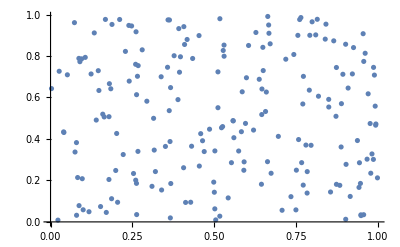

```mathematica
(*23.3 A plot of 200 points with random real x and y coordinates between 0 and 1.*)
ListPlot[Table[{RandomReal[1],RandomReal[1]},200]]
```

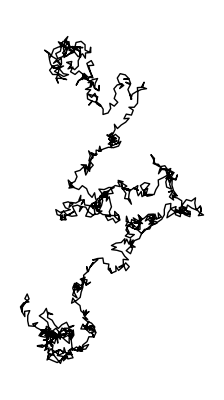

```mathematica
(*23.4 A random walk using AnglePath and 1000 random real numbers between 0 and 2π *)
Graphics[Line[AnglePath[Table[RandomReal[2Pi],1000]]]]
```

```mathematica
(*23.5 Table of Mod[n^2,10]for n from 0 to 30*)
Table[Mod[n^2,10], {n, 0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

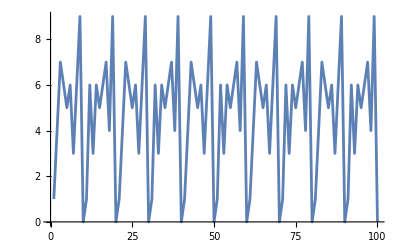

```mathematica
(*23.6 Line plot of Mod[n^n,10] for n from 1 to 100.*)
ListLinePlot[Table[Mod[n^n,10],{n,1,100}]]
```

```mathematica
(*23.7 Table of the first 10 powers of pi, rounded to integers*)
Table[Round[π^n], {n, 1,10}]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

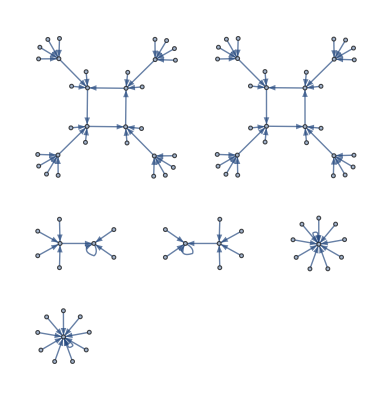

```mathematica
(*23.8 A graph by connecting n with Mod[n^2,100] for n from 0 to 99*)
Graph[Table[n-> Mod[n^2,100],{n,0,99}]]
```

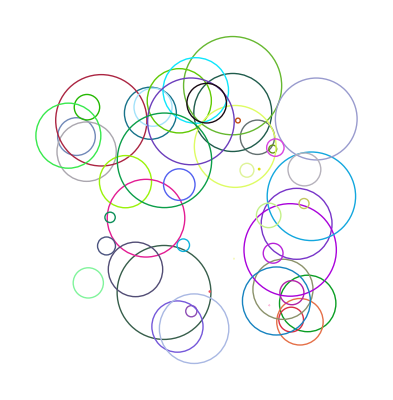

```mathematica
(*23.9 Graphics of 50 circles with random real coordinates 0 to 10,random real radii from 0 to 2,and random colors.*)
Graphics[Table[Style[Circle[{RandomReal[10],RandomReal[10]},RandomReal[2]],RandomColor[]],50]]
```

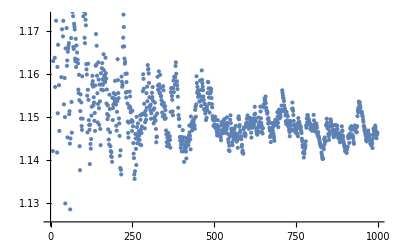

```mathematica
(*23.10 A plot of the nth prime divided by n*log(n),for n from 2 to 1000*)
ListPlot[Table[Prime[n]/(n*Log[n]),{n,2,1000}]]
```

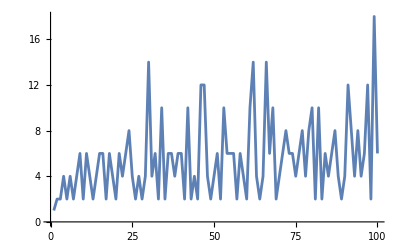

```mathematica
(*23.11 Line plot of the diffrences between sucessive primes up to 100*)
ListLinePlot[Table[Prime[n+1]-Prime[n],{n,1,100}]]
```

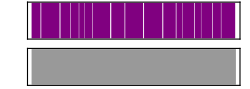

```mathematica
(*23.12 A squence of 20 middle C notes with random durations between 0 to 0.5 seconds*)
Sound[Table[SoundNote["C", RandomReal[.5]],20]]
```

```mathematica
(*23.13 An array plot of Mod[i,j] for i and j up to 50 *)
ArrayPlot[Table[Mod[i,j],{i,1,50},{j,1,50}]]
```

-Graphics-

```mathematica
(*23.14 A list for n from 2 to 10 of array plots of x and y up to 50 of x^y mod n*)
Table[ArrayPlot[Table[Mod[x^y,n],{x,1,50},{y,1,50}]],{n,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Section 24

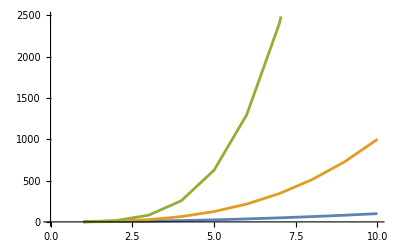

```mathematica
(*24.1 Plot with lines joining the squares, the cubes and the 4th powers of integers up to 10.*)
ListLinePlot[{Table[x^2,{x,1,10}], Table[x^3, {x,1,10}], Table[x^4,{x,1,10}]} ]
```

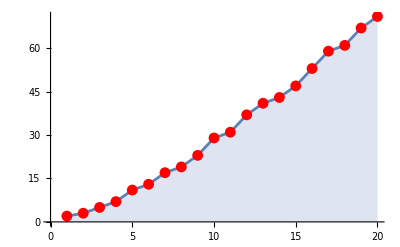

```mathematica
(*24.2 Plot the first 20 primes, joined by a lin, filled to the axis and with a red dot at each prime*)
ListLinePlot[Table[Prime[n],{n,1,20}], Filling->Axis, Mesh->All, MeshStyle->Red]
```

```mathematica
(*24.3 3D plot of the topography for 20 miles around Mount Fuji*)
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[20, "Miles"]]]]
```

-Graphics3D-

```mathematica
(*24.4 A relief plot of the topography for 100 miles around Mount Fuji.*)
ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[100, "Miles"]]]]
```

-Graphics-

```mathematica
(*24.5 A 3D plot of heights generated from Mod[i,j] with i and j going up to 100.*)
ListPlot3D[Table[Mod[i,j],{i,1,100},{j,1,100}]]
```

-Graphics3D-

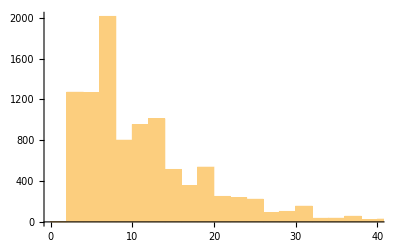

```mathematica
(*24.6 Histogram of the differences between successive primes for the first 10000 primes*)
Histogram[Table[Prime[n+1]-Prime[n],{n,1,10000}]]
```

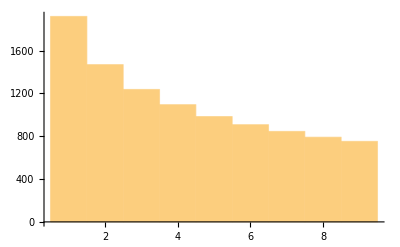

```mathematica
(*24.7 A histogram of the first digits of squares of integers up to 10000 (illustrating Benford’s law).*)
Histogram[Flatten[Table[Take[IntegerDigits[x^2],1],{x,1,10000}]]]
```

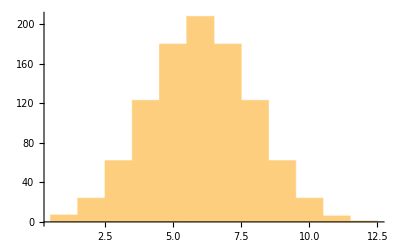

```mathematica
(*24.8 A histogram of the length of Roman numerals up to 1000.*)
Histogram[Table[StringLength[RomanNumeral[n]],{n,1,1000}]]
```

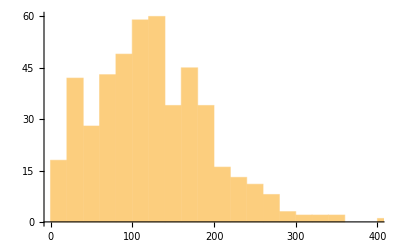

```mathematica
(*24.9 A histogram of sentence lengths in the Wikipedia article on computers.*)
Histogram[StringLength[TextSentences[WikipediaData["computers"]]]]
```

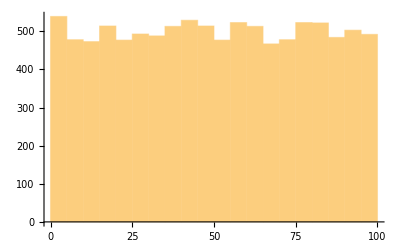
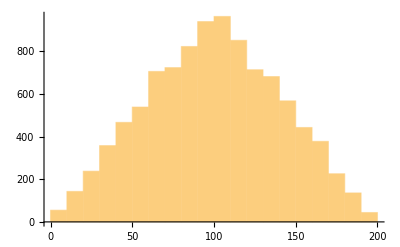
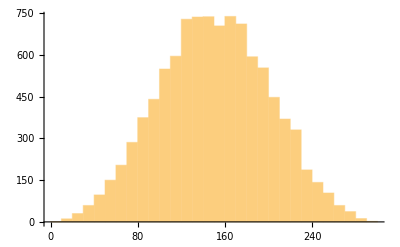
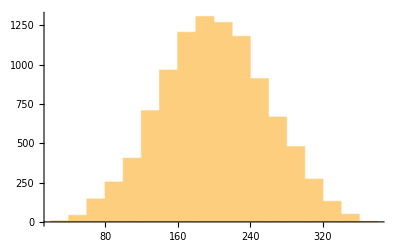
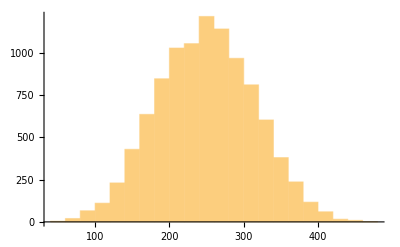

```mathematica
(*24.10 A list of histograms of 10000 instances of totals of n random reals up to 100,with n going from 1 to 5 (illustrating the central limit theorem*)
Table[Histogram[Table[Total[RandomReal[100,n] ],10000]] ,{n,1,5}]
```

```mathematica
(*24.11 Generate a 3D list plot using the image data from a binarized size-200 letter “W” as heights*)
ListPlot3D[ImageData[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

## Section 24

Some notes because Wolfram didn’t really:
/@: apply the previous thing to all elements in list following it
&: indicates the previous is a pure function
#: “slot” in which element is put  (if it’s followed /@ it will each element into the list)
EXAMPLE:
Rotate[#, 90 degree] &/@{“one”, “two”, “three”]  -> Rotate[one, 90 degree], Rotate[two, 90 degree]...
vs. 
Rotate[“hello”, #] &/@[30 deg, 90 deg, 80 deg] -> Rotate[“hello”, 30 degree], Rotate[“hello”, 90 degree]...
#: can also be used to pair
{#, ColorNegate[#]}&/@{Red, Blue, Green}

```mathematica
(*26.1 Use Range and a pure function to create a list of the first 20 squares.*)
Power[#,2]&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
(*26.2 A list of the result of blending yellow,green and blue with red*)
Blend[{#,Red}]&/@ {Yellow, Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
(*26.3 Generate a list of framed columns containing the uppercase and lowercase versions of each letter of the alphabet.*)
Framed[Column[{ToUpperCase[#], #}]]&/@ Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
(*26.4 A list of letters of the alphabet,in random colors,with frames having random background colors.*)
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}






{France | -Graphics-,Germany | -Graphics-,Japan | -Graphics-,United Kingdom | -Graphics-,United States | -Graphics-}

```mathematica
(*26.5 A table of G5 countries,together with their flags,and arrange the result in a fully framed grid.*)
Framed[Grid[Table[{#,CountryData[#,"Flag"]},1]]]&/@EntityList[EntityClass["Country","GroupOf5"]]
```

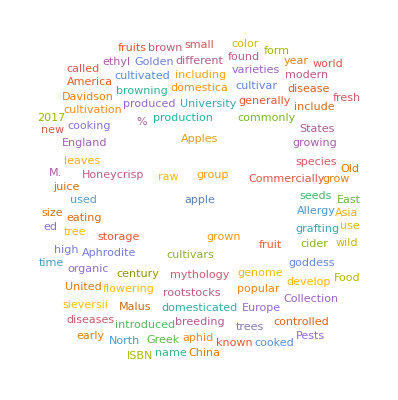
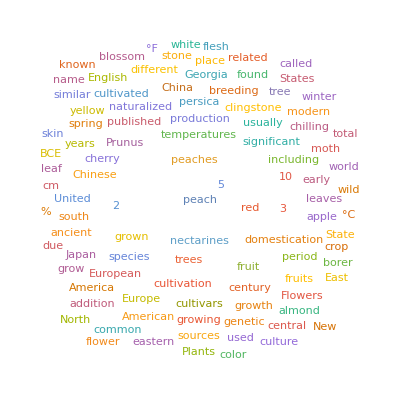
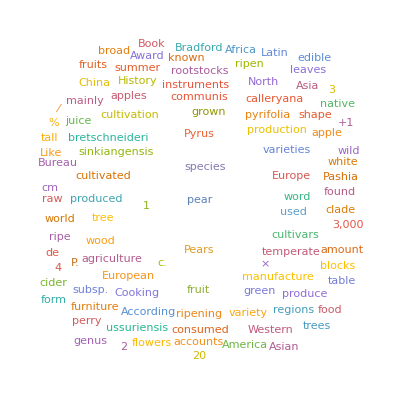

```mathematica
(**)
WordCloud[WikipediaData[#]]&/@{"apple", "peach", "pear"}
```

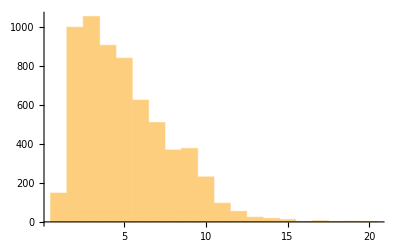
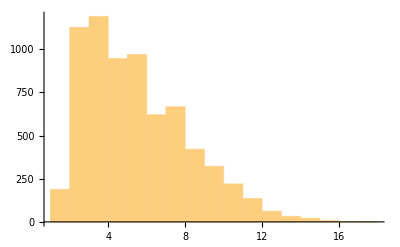
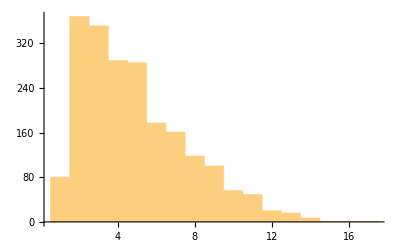

```mathematica
(* 26.7 List of histograms of the word lengths in Wikipedia articles on apple,peach and pear.*)
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach", "pear"}
```

```mathematica
(*26.8 A list of maps of Central America,highlighting each country in turn*)GeoListPlot[#, GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}